```mathematica
PlotSurf[surffname_]:=Module[{surfs,surfshapes},
surfs=Import[surffname, "Table",HeaderLines->9, "FieldSeperators"->" ", "LineSeperators"->"\n"];
surfshapes=Flatten@Table[Line[{{s[[2]],s[[3]]},{s[[4]],s[[5]]}}],{s,surfs}];
Graphics[Join[{Directive[{Thin,Red}]},surfshapes],ImageSize->Large]
]
```

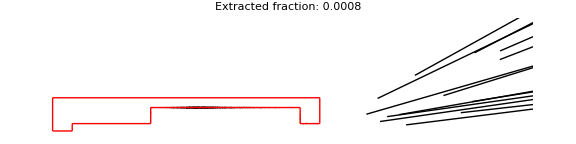

```mathematica
dir="/home/cal/Documents/DSMC_Simulations/4_8_20_Yuiki_cell/2sccm/data/";
(*dir="/home/cal/Documents/DSMC_Simulations/4_3_20_flow_gap_length/flow_10.000_gap_0.004_len_0.013/data/";*)
data=Import[StringJoin[dir,"particles.out"],"Table",HeaderLines->1];
flow=Import[StringJoin[dir,"DS2FF.500000.DAT"],"Table",HeaderLines->9];
surfs=PlotSurf[StringJoin[dir,"cell.510000.surfs"]];
flow=Select[flow,#[[3]]>0&];
z=data[[;;,3]];
y=data[[;;,2]];
x=data[[;;,1]];
outside=Position[z,x_/;x>0.09];
r=√(data[[;;,1]]^2+data[[;;,2]]^2);
znext=data[[;;,6]];
ynext=data[[;;,5]];
xnext=data[[;;,4]];
rnext=√(data[[;;,4]]^2+data[[;;,5]]^2);
vx=data[[;;,7]];
vy=data[[;;,8]];
vz=data[[;;,9]];
v=√(vx^2+vy^2+vz^2);
collides=data[[;;,-2]];
times=data[[;;,-1]];
lines=Table[Line[{{z[[i]],r[[i]]},{znext[[i]],rnext[[i]]}}],{i,Length@data}];
extraction=N[Length@outside/Length@z];
trajs=Show[Graphics[{Thin,lines},PlotRange->{{0,0.12},{0,0.03}},PlotLabel->StringForm["Extracted fraction: ``",extraction]],surfs,ImageSize->Large]
```

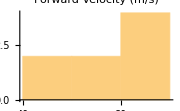
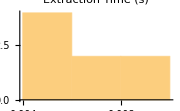
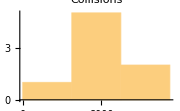

```mathematica
Row[{Histogram[vz[[Flatten[outside]]],PlotLabel->"Forward Velocity (m/s)",ImageSize->Small],
Histogram[times[[Flatten[outside]]],
PlotLabel->"Extraction Time (s)",ImageSize->Small],
Histogram[collides[[Flatten[outside]]],
PlotLabel->"Collisions",ImageSize->Small]}]
```

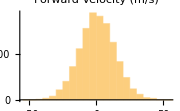
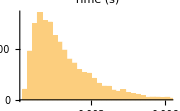
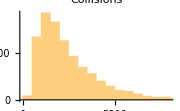

```mathematica
Row[{Histogram[vz,PlotLabel->"Forward Velocity (m/s)",ImageSize->Small],
Histogram[times,
PlotLabel->"Time (s)",ImageSize->Small],
Histogram[collides,
PlotLabel->"Collisions",ImageSize->Small]}]
```

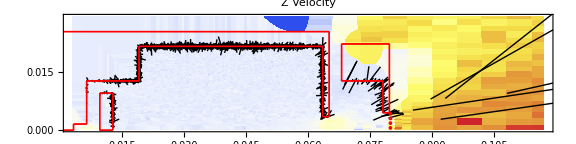

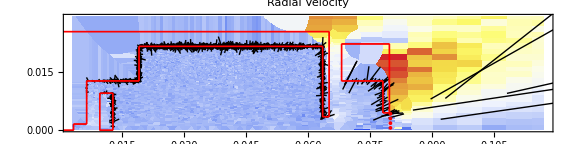

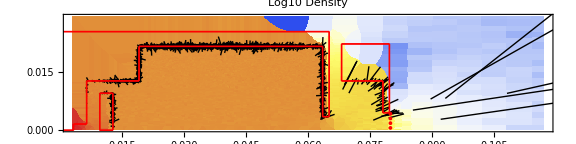

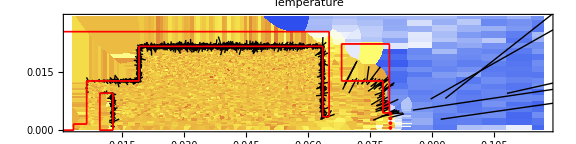

```mathematica
Show[ListDensityPlot[flow[[;;,{1,2,6}]],ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Z Velocity",ColorFunction->"TemperatureMap",PlotRange->All],trajs,surfs]
Show[ListDensityPlot[flow[[;;,{1,2,7}]],ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Radial Velocity",ColorFunction->"TemperatureMap",PlotRange->All],trajs,surfs]
Show[ListDensityPlot[Transpose@{flow[[;;,1]],flow[[;;,2]],Log10[flow[[;;,4]]]},ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Log10 Density",PlotRange->All,
ColorFunction->"TemperatureMap"],trajs,surfs]
Show[ListDensityPlot[flow[[;;,{1,2,3}]],ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Temperature",PlotRange->All,
ColorFunction->"TemperatureMap"],trajs,surfs]
```